# Combine plots of SFOPT with Scalar Extension

```mathematica
ClearAll["Global`*"]
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

## SFOPT bound for v_R=20 TeV

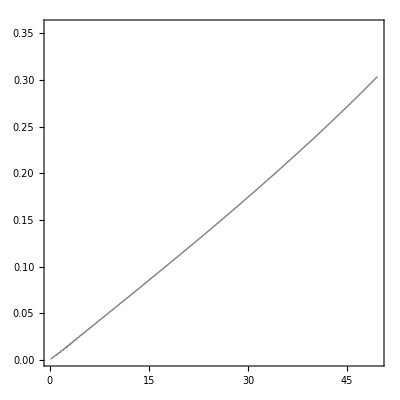

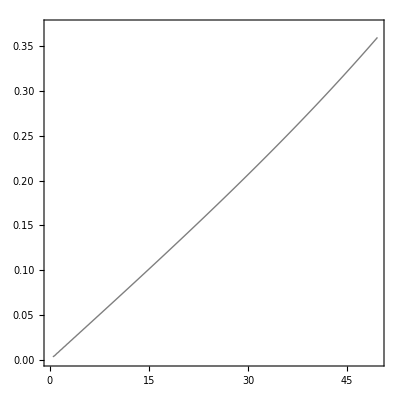

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

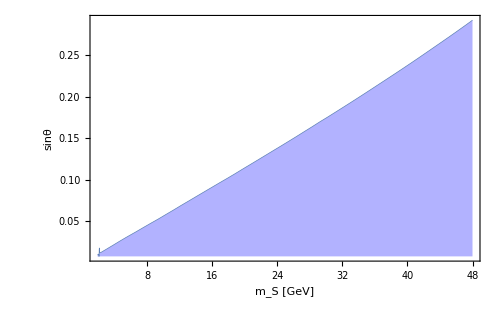

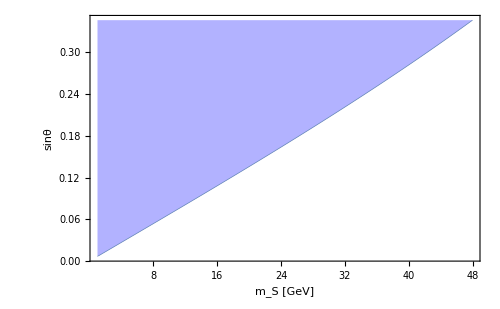

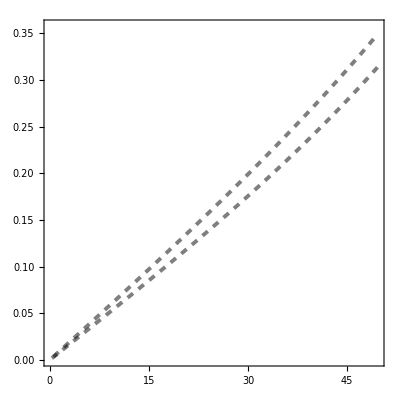

```mathematica
GeVdata‵20=Import[NotebookDirectory[]<>"GeV-SFOPTbound-15TeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[GeVdata‵20,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@GeVdata‵20;
finetunedata={#1,#2,#4/#5}&@@@Select[GeVdata‵20,#[[3]]>0.5&&#[[4]]>0 &];
GeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full]
SFOPTbound=Cases[Normal@GeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->2][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->1][mS]
GeVSFOPTplot‵20=Plot[SFOPTboundfunc[mS],{mS,1.9,48},Filling->Bottom,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->22],Style["sinθ",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
GeVstabilityplot‵20=Plot[stabilityboundfunc[mS],{mS,1.,48},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->22],Style["sinθ",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
finetune20=ListContourPlot[finetunedata,Contours->{0.05,0.2},ContourStyle->Directive[Dashed,Black,Thickness[0.007]],ContourShading->None]
```

## v_R=10^5 GeV

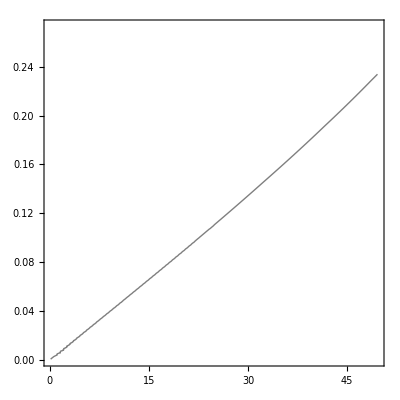

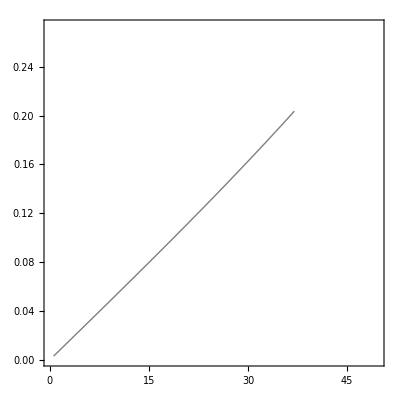

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

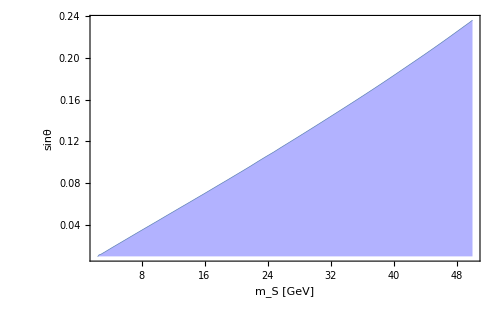

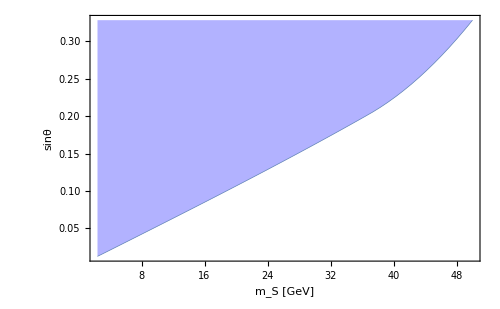

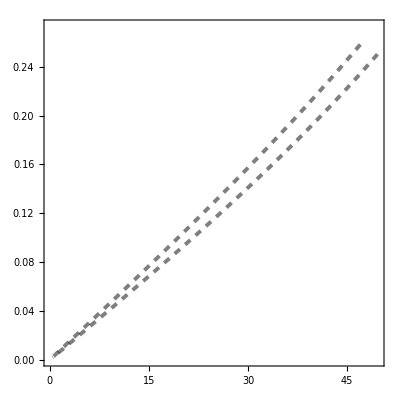

```mathematica
GeVdata‵5=Import[NotebookDirectory[]<>"GeV-SFOPTbound-10^5GeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[GeVdata‵5,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@GeVdata‵5;
finetunedata={#1,#2,#4/#5}&@@@Select[GeVdata‵5,#[[3]]>0.5&&#[[4]]>0 &];
GeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full]
SFOPTbound=Cases[Normal@GeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->1][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->2][mS]
GeVSFOPTplot‵5=Plot[SFOPTboundfunc[mS],{mS,2.414,50},Filling->Bottom,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->22],Style["sinθ",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
GeVstabilityplot‵5=Plot[stabilityboundfunc[mS],{mS,2.414,50},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->22],Style["sinθ",FontFamily->"Times",FontSize->22]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->22],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
finetune5=ListContourPlot[finetunedata,Contours->{0.05,0.2},ContourStyle->Directive[Dashed,Black,Thickness[0.007]],ContourShading->None]
```

## LEP Probes

### 1996 Data

Model-independent production channel.

InterpolatingFunction[…][mS]

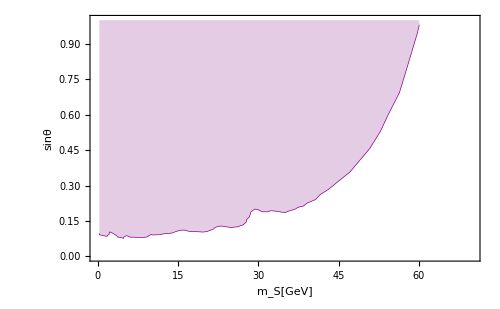

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"LEP1996.csv"];
LEP1996func[mS_]=Interpolation[LEP1996data,InterpolationOrder->1][mS]
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]],PlotRange->{{0,70},{0,1}},FillingStyle->Opacity[0.2]]
```

### 2003 ALEPH

Model-dependent, depending on the decay channel. The main contribution is from the bb decay.

```mathematica
mb=4.19;
mc=1.27;
mτ=1.78;
bBR[mS_]:=(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
cBR[mS_]:=(3 mc^2 Re[(mS^2-4 mc^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
bblimit[mS_]=Interpolation[Import[NotebookDirectory[]<>"LEP-ALEPH.csv"],InterpolationOrder->1][mS]
```

InterpolatingFunction[…][mS]

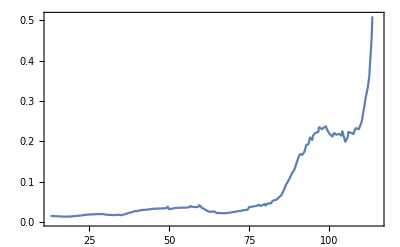

```mathematica
Plot[bblimit[mS],{mS,13,115}]
```

```mathematica
bb‵bound[mS_/;mS>=12.4]=√(bblimit[ mS]/bBR[mS]);
```

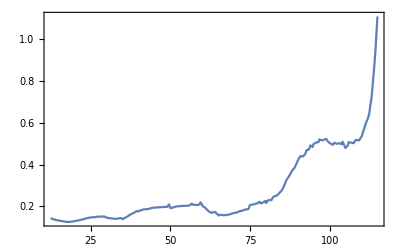

```mathematica
Plot[bb‵bound[mS],{mS,12.4,115}]
```

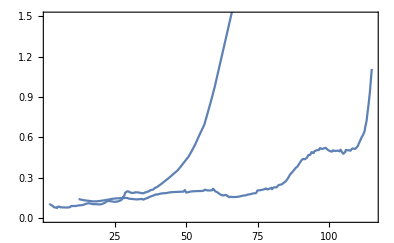

```mathematica
Show[{Plot[LEP1996func[mS],{mS,2.2,68.1}],Plot[bb‵bound[mS],{mS,12.4,115}]},PlotRange->{{2.3,115},{0,1.5}}]
```

```mathematica
Combinebound[mS_/;12.4<=mS<=68.1]:=Min[LEP1996func[mS],bb‵bound[mS]]
Combinebound[mS_/;mS<12.4]:=LEP1996func[mS]
Combinebound[mS_/;mS>68.1]:=bb‵bound[mS]
```

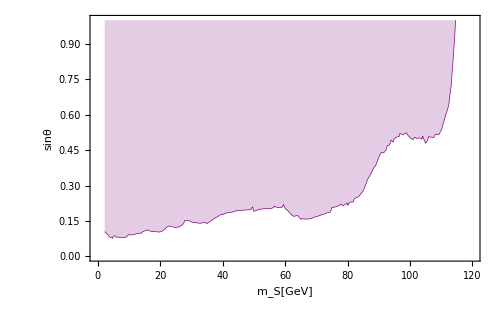

```mathematica
LEP=Plot[Combinebound[mS],{mS,2.3,115},Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]],PlotRange->{{0,120},{0,1}},FillingStyle->Opacity[0.2]]
```

## LHCb

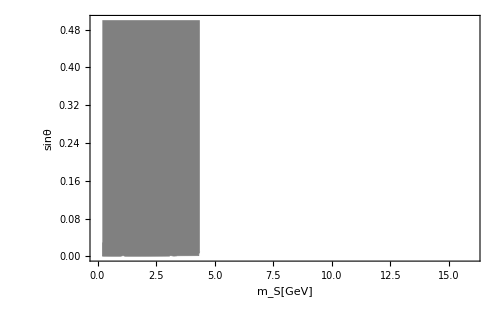

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"LHCb.csv"];
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Gray,Thickness[0.001]],PlotRange->{{0,16},{0,0.5}},FillingStyle->Opacity[1]]
```

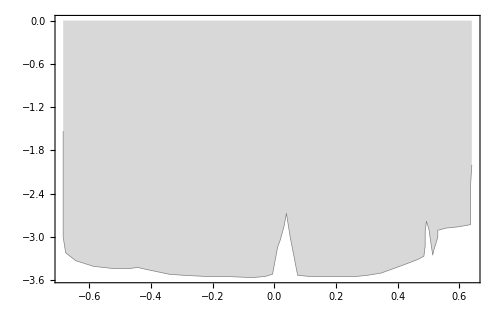

```mathematica
LHCbMeV={Log10[#1],Log10[#2]}&@@@LHCbdata;
LHCbMeVPlot=ListLinePlot[LHCbMeV,PlotStyle->Directive[Gray,Thickness[0.001]],Filling->Top,FillingStyle->Opacity[0.3]]
```

## Exotic Decay

```mathematica
v=246;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
ghSS[mS_,sinθ_]:=A[mS,sinθ]sinθ+6λhL[mS,sinθ]v sinθ^2;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
```

```mathematica
prospectdata=Import[NotebookDirectory[]<>"../probe/Exoticdecay.csv"];
prospectfunc[mS_]:=Interpolation[prospectdata][mS];
Currentdata1=Import[NotebookDirectory[]<>"../probe/ExoticDecayCurrent1.csv"];
Currentdata2=Import[NotebookDirectory[]<>"../probe/ExoticDecayCurrent2.csv"];
Higgsfactorydata=Import[NotebookDirectory[]<>"../probe/Higgsfactory.csv"];
Higgsfactoryfunc[mS_]:=Interpolation[Higgsfactorydata][mS]
Higgsfactorydata2=Import[NotebookDirectory[]<>"../probe/Higgsfactory02.csv"];
Higgsfactoryfunc2[mS_]:=Interpolation[Higgsfactorydata2][mS]
Currentfunc1[mS_]:=Interpolation[Currentdata1][mS];
Currentfunc2[mS_]:=Interpolation[Currentdata2][mS];
```

```mathematica
Higgsfactoryfunc2[mS]
```

InterpolatingFunction[…][mS]

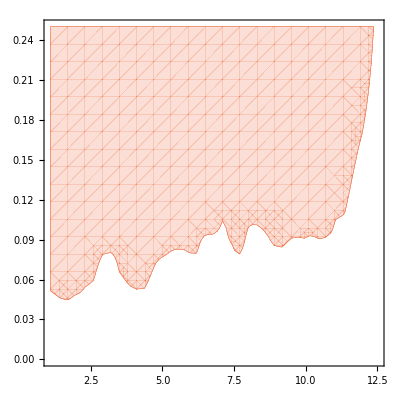

```mathematica
exotic1=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc1[mS],{mS,1.1,12.5},{sinθ,0,0.25},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]]
```

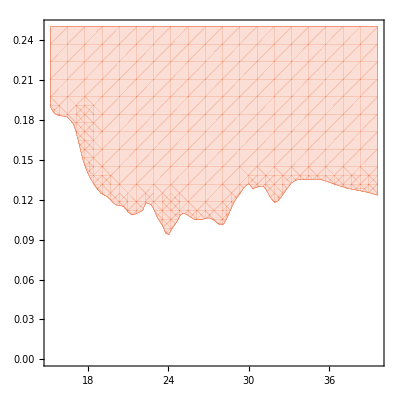

```mathematica
exotic2=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc2[mS],{mS,15.2,39.6},{sinθ,0,0.25},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]]
```

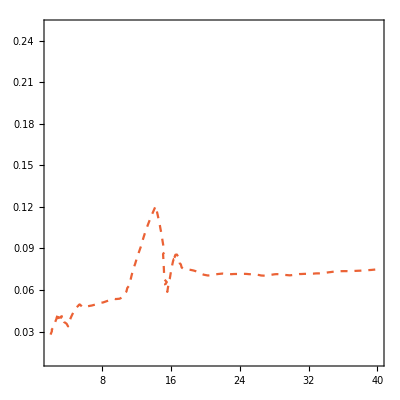

```mathematica
exoticprosp=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,2,40},{sinθ,0.01,0.25},ContourStyle->Directive[Dashed,ColorData[97,4]]]
```

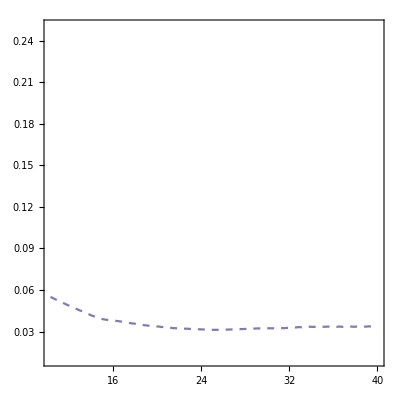

```mathematica
Higgsfactory=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.01,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]]
```

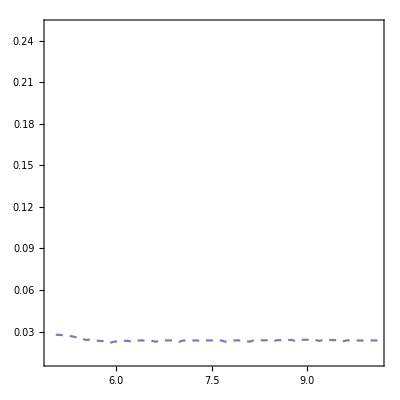

```mathematica
Higgsfactory2=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.01,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]]
```

```mathematica
Currentfunc2[mS]
```

InterpolatingFunction[…][mS]

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Combine

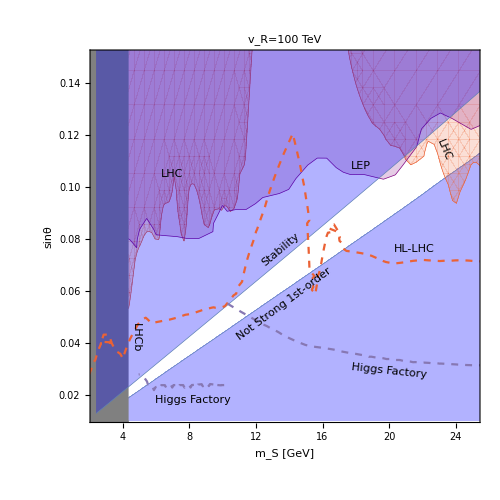

```mathematica
Show[{GeVSFOPTplot‵5,exotic1,exotic2,LEP,LHCb,GeVstabilityplot‵5,exoticprosp,Higgsfactory,Higgsfactory2},PlotRange->{{2.5,25},{0.012,0.15}},AspectRatio->1,PlotLabel->Style["v_R=100 TeV"],Epilog->{Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{18.3,0.108}],Inset[Rotate[Framed[Style["Not Strong 1st-order",FontSize->22,Blue],FrameStyle->None],36.5Degree],{13.7,0.055}],Inset[Rotate[Framed[Style["LHCb",Gray,FontSize->20,FontFamily->"Times"],FrameStyle->None],-90 Degree],{4.8,0.042}],Inset[Rotate[Framed[Style["Stability", FontSize->20,FontFamily->"Times",Blue,FontSize->22],FrameStyle->None],40Degree],{13.5,0.076}],Inset[Rotate[Framed[Style["LHC",ColorData[97,4],FontSize->22],FrameStyle->None],-67Degree],{23.3,0.114}],Inset[Framed[Style["LHC",ColorData[97,13],FontSize->22],FrameStyle->None],{7,0.105}],Inset[Framed[Style["HL-LHC",ColorData[97,4],FontSize->22],FrameStyle->None],{21.5,0.076}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],-6Degree],{20,0.029}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{8.2,0.018}]}]
```

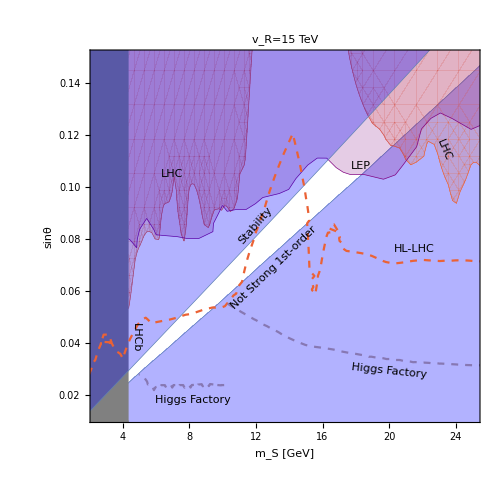

```mathematica
Show[{GeVSFOPTplot‵20,exotic1,exotic2,LEP,LHCb,GeVstabilityplot‵20,exoticprosp,Higgsfactory,Higgsfactory2},PlotRange->{{2.5,25},{0.012,0.15}},AspectRatio->1,PlotLabel->Style["v_R=15 TeV"],Epilog->{Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{18.3,0.108}],Inset[Rotate[Framed[Style["Not Strong 1st-order",FontSize->22,Blue],FrameStyle->None],44.Degree],{13.1,0.069}],Inset[Rotate[Framed[Style["LHCb",Gray,FontSize->20,FontFamily->"Times"],FrameStyle->None],-90 Degree],{4.8,0.042}],Inset[Rotate[Framed[Style["Stability", FontSize->20,FontFamily->"Times",Blue,FontSize->22],FrameStyle->None],49Degree],{12.,0.085}],Inset[Rotate[Framed[Style["LHC",ColorData[97,4],FontSize->22],FrameStyle->None],-67Degree],{23.3,0.114}],Inset[Framed[Style["LHC",ColorData[97,13],FontSize->22],FrameStyle->None],{7,0.105}],Inset[Framed[Style["HL-LHC",ColorData[97,4],FontSize->22],FrameStyle->None],{21.5,0.076}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],-6Degree],{20,0.029}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{8.2,0.018}]}]
```